```mathematica
i:=ⅈ
Subscript[a, 0]:=(4π*ϵ*ℏ^2)/(μ*e^2)
Subscript[E, n_]:=-ℏ^2/(2μ*Subscript[a, 0]^2*n^2)
```

```mathematica
Subscript[E, n]
```

-(e^4 μ)/(32 n^2 π^2 ϵ^2 ℏ^2)

```mathematica
Subscript[P, l_, m_][z_]:=With[{x=z}, Evaluate[(-1)^m/(2^l l!)*(1-x^2)^(m/2)*D[(x^2-1)^l,{x,l+m}]]]
Subscript[Y, l_,m_][θ,ϕ]:= Sqrt[((l-m)!(2l+1))/(4π(l+m)!)]*Subscript[P, l,m][Cos[θ]]*Exp[i*m*ϕ]
Subscript[Δ, angular][f_] := 1/Sin[θ]*D[Sin[θ]*D[f,θ],θ]+1/(Sin[θ])^2*D[f,{ϕ,2}]
Δ[f_] := 1/r^2(D[r^2*D[f,r],r]+Subscript[Δ, angular][f])
```

```mathematica
Subscript[L̂, z][f_]:=-i*ℏ*D[f,ϕ]
Subscript[L̂, 2][f_]:=-ℏ^2*Subscript[Δ, angular][f]
```

```mathematica
(Subscript[L̂, z][Subscript[Y, l,m][θ,ϕ]])/(Subscript[Y, l,m][θ,ϕ])
```

m ℏ

```mathematica
TrigExpand[(Subscript[L̂, 2][Subscript[Y, 3,-2][θ,ϕ]])/(Subscript[Y, 3,-2][θ,ϕ])]
```

12 ℏ^2

```mathematica
Subscript[Lag, n_][z_]:= With[{x=z},Evaluate[Exp[x]*D[Exp[-x]*x^n,{x, n}]]]
Subscript[Lag, α_,n_][z_]:=With[{x=z},Evaluate[(-1)^α*D[Subscript[Lag, n+α][x],{x,α}]]]
```

```mathematica
Subscript[R, n_,l_][r_]:=√((2/(n*Subscript[a, 0]))^3*((n-l-1)!)/(2n((n+l)!)^3))*With[{x=(2r)/(n*Subscript[a, 0])},Exp[-1/2 x]*x^l*Subscript[Lag, (2l+1),(n-l-1)][x]]
```

```mathematica
Subscript[Schrod, n_,l_][f_]:=D[r^2*D[f,r],r] + ((2r)/Subscript[a, 0]-r^2/(Subscript[a, 0]^2 n^2)-l(1+l))*f
```

```mathematica
Subscript[Schrod, n_][f_]:=ℏ^2/(2μ)Δ[f]+(e^2/(4π*ϵ*r)+Subscript[E, n])*f
```

```mathematica
Subscript[CSchrod, R][n_, l_] :=Together[ExpandAll[Subscript[Schrod, n,l][Subscript[R, n,l][r]]]]
```

```mathematica
Subscript[CSchrod, R][3,2]
```

0

```mathematica
CSchrod[n_,l_, m_] :=Expand[TrigExpand[Subscript[Schrod, n][Subscript[R, n,l][r]*Subscript[Y, l,m][θ,ϕ]]]]
```

```mathematica
CSchrod[5,2,1]
```

0

```mathematica
N[Integrate[Subscript[Y, 2,2][θ,ϕ]*(Subscript[Y, 2,2][θ,ϕ])* * Sin[θ],{θ,0,π},{ϕ,0,2π}]]
```

1.

```mathematica
N[NIntegrate[With[{ℏ= 1,μ=0.0005,e=0.301,ϵ=1},Evaluate[Subscript[R, 1,0][r]*Subscript[R, 1,0][r]**r^2]],{r,0,10000000},AccuracyGoal->10]]
```

1.

```mathematica
N[Integrate[With[{ℏ= 1,μ=0.00051,e=0.301,ϵ=1},Evaluate[Subscript[R, 1,0][r]*Subscript[R, 1,0][r]**r^3]],{r,0,10000000}]]
```

407942.

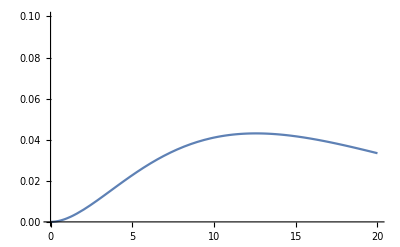

```mathematica
f[r_] :=Evaluate[With[{ℏ= 1,μ=1,e=1,ϵ=1},Evaluate[Expand[(Subscript[R, 1,0][r])^2*r^2]]]]
Plot[f[r],{r,0,20}, PlotRange->{{0,20},{0,0.1}}]
```

```mathematica
Subscript[A, l_,m_][u_] := ((l-m)!(2l+1))/(4π(l+m)!)*(Subscript[P, l,m][u])^2
```

```mathematica
h[x_,z_]:=With[{n=4,l=2,m=1},(Subscript[R, n,l][√(x^2+z^2)])^2*Subscript[A, l,m][z/√(x^2+z^2)]]
g[x_,z_]:=Evaluate[With[{ℏ= 1,μ=1,e=1,ϵ=1/(4π)},Evaluate[h[x,z]]]]
```

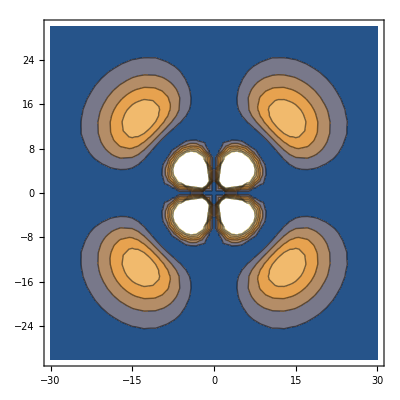

```mathematica
ContourPlot[g[x,z],{x,-30,30},{z,-30,30}, PlotRange->Automatic]
```

```mathematica
ExpandAll[With[{ℏ= 1,μ=1,e=1,ϵ=1/(4π)},Evaluate[h[x,z]]]]
```

(ⅇ^(-1/2 √(x^2+z^2)) x^6)/(37748736 π)+(ⅇ^(-1/2 √(x^2+z^2)) x^4 z^2)/(12582912 π)+(ⅇ^(-1/2 √(x^2+z^2)) x^2 z^4)/(12582912 π)+(ⅇ^(-1/2 √(x^2+z^2)) z^6)/(37748736 π)-(ⅇ^(-1/2 √(x^2+z^2)) x^6 z^6)/(37748736 π (x^2+z^2)^3)-(ⅇ^(-1/2 √(x^2+z^2)) x^4 z^8)/(12582912 π (x^2+z^2)^3)-(ⅇ^(-1/2 √(x^2+z^2)) x^2 z^10)/(12582912 π (x^2+z^2)^3)-(ⅇ^(-1/2 √(x^2+z^2)) z^12)/(37748736 π (x^2+z^2)^3)+(ⅇ^(-1/2 √(x^2+z^2)) x^6 z^4)/(12582912 π (x^2+z^2)^2)+(ⅇ^(-1/2 √(x^2+z^2)) x^4 z^6)/(4194304 π (x^2+z^2)^2)+(ⅇ^(-1/2 √(x^2+z^2)) x^2 z^8)/(4194304 π (x^2+z^2)^2)+(ⅇ^(-1/2 √(x^2+z^2)) z^10)/(12582912 π (x^2+z^2)^2)-(ⅇ^(-1/2 √(x^2+z^2)) x^6 z^2)/(12582912 π (x^2+z^2))-(ⅇ^(-1/2 √(x^2+z^2)) x^4 z^4)/(4194304 π (x^2+z^2))-(ⅇ^(-1/2 √(x^2+z^2)) x^2 z^6)/(4194304 π (x^2+z^2))-(ⅇ^(-1/2 √(x^2+z^2)) z^8)/(12582912 π (x^2+z^2))

```mathematica
ExpandAll[With[{n=9,l=7,m=5},(Subscript[R, n,l][r]*Subscript[Y, l,m][θ,ϕ])]]
```

-(e^16 ⅇ^(5 ⅈ ϕ-(e^2 r μ)/(36 π ϵ ℏ^2)) r^8 μ^8 √((e^6 μ^3)/(ϵ^3 ℏ^6)) √(1-Cos[θ]^2))/(2632434076845342720 √91 π^10 ϵ^8 ℏ^16)+(e^14 ⅇ^(5 ⅈ ϕ-(e^2 r μ)/(36 π ϵ ℏ^2)) r^7 μ^7 √((e^6 μ^3)/(ϵ^3 ℏ^6)) √(1-Cos[θ]^2))/(9140396100157440 √91 π^9 ϵ^7 ℏ^14)+(e^16 ⅇ^(5 ⅈ ϕ-(e^2 r μ)/(36 π ϵ ℏ^2)) r^8 μ^8 √((e^6 μ^3)/(ϵ^3 ℏ^6)) Cos[θ]^2 √(1-Cos[θ]^2))/(175495605123022848 √91 π^10 ϵ^8 ℏ^16)-(e^14 ⅇ^(5 ⅈ ϕ-(e^2 r μ)/(36 π ϵ ℏ^2)) r^7 μ^7 √((e^6 μ^3)/(ϵ^3 ℏ^6)) Cos[θ]^2 √(1-Cos[θ]^2))/(609359740010496 √91 π^9 ϵ^7 ℏ^14)-(e^16 ⅇ^(5 ⅈ ϕ-(e^2 r μ)/(36 π ϵ ℏ^2)) r^8 μ^8 √((e^6 μ^3)/(ϵ^3 ℏ^6)) Cos[θ]^4 √(1-Cos[θ]^2))/(97497558401679360 √91 π^10 ϵ^8 ℏ^16)+(e^14 ⅇ^(5 ⅈ ϕ-(e^2 r μ)/(36 π ϵ ℏ^2)) r^7 μ^7 √((e^6 μ^3)/(ϵ^3 ℏ^6)) Cos[θ]^4 √(1-Cos[θ]^2))/(338533188894720 √91 π^9 ϵ^7 ℏ^14)+(√(13/7) e^16 ⅇ^(5 ⅈ ϕ-(e^2 r μ)/(36 π ϵ ℏ^2)) r^8 μ^8 √((e^6 μ^3)/(ϵ^3 ℏ^6)) Cos[θ]^6 √(1-Cos[θ]^2))/(2632434076845342720 π^10 ϵ^8 ℏ^16)-(√(13/7) e^14 ⅇ^(5 ⅈ ϕ-(e^2 r μ)/(36 π ϵ ℏ^2)) r^7 μ^7 √((e^6 μ^3)/(ϵ^3 ℏ^6)) Cos[θ]^6 √(1-Cos[θ]^2))/(9140396100157440 π^9 ϵ^7 ℏ^14)